```mathematica
{x->ϵ, y->η,z-> ζ}
```

{x→ϵ,y→η,z→ζ}

```mathematica
TetrahedronTransform={
x1 + (x2 - x1)* ϵ + (x3-x1) *η+ (x4-x1)*ζ, y1 + (y2 - y1)* ϵ + (y3-y1) *η+ (y4-y1)*ζ, z1 + (z2 - z1)* ϵ + (z3-z1) *η+ (z4-z1)*ζ
}
```

{x1+(-x1+x2) ϵ+(-x1+x4) ζ+(-x1+x3) η,y1+(-y1+y2) ϵ+(-y1+y4) ζ+(-y1+y3) η,z1+(-z1+z2) ϵ+(-z1+z4) ζ+(-z1+z3) η}

```mathematica
coordTransform[pt_List,transform_,var_:Automatic]:=Module[{v,f},v=If[var===Automatic,Variables[Level[transform,{-1}]],var];
f=Function@@{v,transform};
f@@pt]
```

```mathematica
coordTransform[{0,0,0},TetrahedronTransform,{ϵ, η, ζ}]
coordTransform[{1,0,0},TetrahedronTransform,{ϵ, η, ζ}]
coordTransform[{0,1,0},TetrahedronTransform,{ϵ, η, ζ}]
coordTransform[{0,0,1},TetrahedronTransform,{ϵ, η, ζ}]
```

{x1,y1,z1}

{x2,y2,z2}

{x3,y3,z3}

{x4,y4,z4}

```mathematica
D[TetrahedronTransform,{{ϵ, η, ζ}}]//MatrixForm
```

(-x1+x2 | -x1+x3 | -x1+x4
-y1+y2 | -y1+y3 | -y1+y4
-z1+z2 | -z1+z3 | -z1+z4)

```mathematica
TetrahedronTransformVar={
x->x1 + (x2 - x1)* ϵ + (x3-x1) *η+ (x4-x1)*ζ, y->y1 + (y2 - y1)* ϵ + (y3-y1) *η+ (y4-y1)*ζ, z->z1 + (z2 - z1)* ϵ + (z3-z1) *η+ (z4-z1)*ζ
}
```

{x→x1+(-x1+x2) ϵ+(-x1+x4) ζ+(-x1+x3) η,y→y1+(-y1+y2) ϵ+(-y1+y4) ζ+(-y1+y3) η,z→z1+(-z1+z2) ϵ+(-z1+z4) ζ+(-z1+z3) η}

```mathematica
J = D[TetrahedronTransform,{{ϵ, η, ζ}}]
J//MatrixForm
```

{{-x1+x2,-x1+x3,-x1+x4},{-y1+y2,-y1+y3,-y1+y4},{-z1+z2,-z1+z3,-z1+z4}}

(-x1+x2 | -x1+x3 | -x1+x4
-y1+y2 | -y1+y3 | -y1+y4
-z1+z2 | -z1+z3 | -z1+z4)

```mathematica
Simplify@Expand@Det[J]
```

-x2 y3 z1+x2 y4 z1+x1 y3 z2-x1 y4 z2+x2 y1 z3-x1 y2 z3+x1 y4 z3-x2 y4 z3+x4 (-y2 z1+y3 z1+y1 z2-y3 z2-y1 z3+y2 z3)-x2 y1 z4+x1 y2 z4-x1 y3 z4+x2 y3 z4+x3 (-y4 z1-y1 z2+y4 z2+y2 (z1-z4)+y1 z4)

```mathematica
(x^2)/.TetrahedronTransformVar
```

(x1+(-x1+x2) ϵ+(-x1+x4) ζ+(-x1+x3) η)^2

```mathematica
Integrate[(x^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]
```

1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))

Inertia Tensor

### ∫x^2dm

```mathematica
IX2 = Simplify@Expand[Integrate[(x^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]]
```

1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))

### ∫y^2dm

```mathematica
IY2 = Simplify@Expand[Integrate[(y^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]]
```

1/12 (y1^2+y2^2+y3^2+2 y3 y4+2 y4^2+y2 (y3+2 y4)-y1 (y2+y3+2 y4))

### ∫z^2dm

```mathematica
IZ2 = Simplify@Expand[Integrate[(z^2)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]]
```

1/12 (z1^2+z2^2+z3^2+2 z3 z4+2 z4^2+z2 (z3+2 z4)-z1 (z2+z3+2 z4))

```mathematica
result =Table[{f,Simplify@Expand[Integrate[(f)/.TetrahedronTransformVar, {ϵ, 0, 1}, {η, 0, 1 - ϵ}, {ζ, 0, 1}]]},{f,{x^2,y^2,z^2, y z, x z, x y}}]
```

{{x^2,1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))},{y^2,1/12 (y1^2+y2^2+y3^2+2 y3 y4+2 y4^2+y2 (y3+2 y4)-y1 (y2+y3+2 y4))},{z^2,1/12 (z1^2+z2^2+z3^2+2 z3 z4+2 z4^2+z2 (z3+2 z4)-z1 (z2+z3+2 z4))},{y z,1/24 (-y3 z1-2 y4 z1+y3 z2+2 y4 z2+2 y3 z3+2 y4 z3+y1 (2 z1-z2-z3-2 z4)+2 y3 z4+4 y4 z4+y2 (-z1+2 z2+z3+2 z4))},{x z,1/24 (-x3 z1-2 x4 z1+x3 z2+2 x4 z2+2 x3 z3+2 x4 z3+x1 (2 z1-z2-z3-2 z4)+2 x3 z4+4 x4 z4+x2 (-z1+2 z2+z3+2 z4))},{x y,1/24 (-x3 y1-2 x4 y1+x3 y2+2 x4 y2+2 x3 y3+2 x4 y3+x1 (2 y1-y2-y3-2 y4)+2 x3 y4+4 x4 y4+x2 (-y1+2 y2+y3+2 y4))}}

```mathematica
substitution = Flatten@Table[ToExpression[StringJoin[ToString[f], ToString[i]]]-> Subscript[f,i], {f,{x,y,z}}, {i,1,4}]
```

{x1→x_1,x2→x_2,x3→x_3,x4→x_4,y1→y_1,y2→y_2,y3→y_3,y4→y_4,z1→z_1,z2→z_2,z3→z_3,z4→z_4}

```mathematica
result/.substitution
```

{{x^2,1/12 (x_1^2+x_2^2+x_3^2+2 x_3 x_4+2 x_4^2+x_2 (x_3+2 x_4)-x_1 (x_2+x_3+2 x_4))},{y^2,1/12 (y_1^2+y_2^2+y_3^2+2 y_3 y_4+2 y_4^2+y_2 (y_3+2 y_4)-y_1 (y_2+y_3+2 y_4))},{z^3,1/120 (-4 z_1^3+6 z_2^3+6 z_3^3+15 z_3^2 z_4+20 z_3 z_4^2+15 z_4^3+3 z_2^2 (2 z_3+5 z_4)+z_1^2 (11 z_2+11 z_3+20 z_4)+z_2 (6 z_3^2+15 z_3 z_4+20 z_4^2)-z_1 (9 z_2^2+9 z_2 z_3+9 z_3^2+25 z_2 z_4+25 z_3 z_4+25 z_4^2))},{y z,1/24 (-y_3 z_1-2 y_4 z_1+y_3 z_2+2 y_4 z_2+2 y_3 z_3+2 y_4 z_3+y_1 (2 z_1-z_2-z_3-2 z_4)+2 y_3 z_4+4 y_4 z_4+y_2 (-z_1+2 z_2+z_3+2 z_4))},{x z,1/24 (-x_3 z_1-2 x_4 z_1+x_3 z_2+2 x_4 z_2+2 x_3 z_3+2 x_4 z_3+x_1 (2 z_1-z_2-z_3-2 z_4)+2 x_3 z_4+4 x_4 z_4+x_2 (-z_1+2 z_2+z_3+2 z_4))},{x y,1/24 (-x_3 y_1-2 x_4 y_1+x_3 y_2+2 x_4 y_2+2 x_3 y_3+2 x_4 y_3+x_1 (2 y_1-y_2-y_3-2 y_4)+2 x_3 y_4+4 x_4 y_4+x_2 (-y_1+2 y_2+y_3+2 y_4))}}

```mathematica
Table[expr[[2]]/.substitution, {expr, result}]
```

{1/12 (x_1^2+x_2^2+x_3^2+2 x_3 x_4+2 x_4^2+x_2 (x_3+2 x_4)-x_1 (x_2+x_3+2 x_4)),1/12 (y_1^2+y_2^2+y_3^2+2 y_3 y_4+2 y_4^2+y_2 (y_3+2 y_4)-y_1 (y_2+y_3+2 y_4)),1/120 (-4 z_1^3+6 z_2^3+6 z_3^3+15 z_3^2 z_4+20 z_3 z_4^2+15 z_4^3+3 z_2^2 (2 z_3+5 z_4)+z_1^2 (11 z_2+11 z_3+20 z_4)+z_2 (6 z_3^2+15 z_3 z_4+20 z_4^2)-z_1 (9 z_2^2+9 z_2 z_3+9 z_3^2+25 z_2 z_4+25 z_3 z_4+25 z_4^2)),1/24 (-y_3 z_1-2 y_4 z_1+y_3 z_2+2 y_4 z_2+2 y_3 z_3+2 y_4 z_3+y_1 (2 z_1-z_2-z_3-2 z_4)+2 y_3 z_4+4 y_4 z_4+y_2 (-z_1+2 z_2+z_3+2 z_4)),1/24 (-x_3 z_1-2 x_4 z_1+x_3 z_2+2 x_4 z_2+2 x_3 z_3+2 x_4 z_3+x_1 (2 z_1-z_2-z_3-2 z_4)+2 x_3 z_4+4 x_4 z_4+x_2 (-z_1+2 z_2+z_3+2 z_4)),1/24 (-x_3 y_1-2 x_4 y_1+x_3 y_2+2 x_4 y_2+2 x_3 y_3+2 x_4 y_3+x_1 (2 y_1-y_2-y_3-2 y_4)+2 x_3 y_4+4 x_4 y_4+x_2 (-y_1+2 y_2+y_3+2 y_4))}

```mathematica
result
```

{{x^2,1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))},{y^2,1/12 (y1^2+y2^2+y3^2+2 y3 y4+2 y4^2+y2 (y3+2 y4)-y1 (y2+y3+2 y4))},{z^2,1/12 (z1^2+z2^2+z3^2+2 z3 z4+2 z4^2+z2 (z3+2 z4)-z1 (z2+z3+2 z4))},{y z,1/24 (-y3 z1-2 y4 z1+y3 z2+2 y4 z2+2 y3 z3+2 y4 z3+y1 (2 z1-z2-z3-2 z4)+2 y3 z4+4 y4 z4+y2 (-z1+2 z2+z3+2 z4))},{x z,1/24 (-x3 z1-2 x4 z1+x3 z2+2 x4 z2+2 x3 z3+2 x4 z3+x1 (2 z1-z2-z3-2 z4)+2 x3 z4+4 x4 z4+x2 (-z1+2 z2+z3+2 z4))},{x y,1/24 (-x3 y1-2 x4 y1+x3 y2+2 x4 y2+2 x3 y3+2 x4 y3+x1 (2 y1-y2-y3-2 y4)+2 x3 y4+4 x4 y4+x2 (-y1+2 y2+y3+2 y4))}}

```mathematica
Collect[result[[6,2]],{x1,x2,x3,x4}]
```

1/24 x1 (2 y1-y2-y3-2 y4)+1/24 x2 (-y1+2 y2+y3+2 y4)+1/24 x3 (-y1+y2+2 y3+2 y4)+1/24 x4 (-2 y1+2 y2+2 y3+4 y4)

```mathematica
Normal[CoefficientArrays[1/24 x1 (2 y1-y2-y3-2 y4)+1/24 x2 (-y1+2 y2+y3+2 y4)+1/24 x3 (-y1+y2+2 y3+2 y4)+1/24 x4 (-2 y1+2 y2+2 y3+4 y4),{x1,x2,x3,x4}]]
```

{0,{1/24 (2 y1-y2-y3-2 y4),1/24 (-y1+2 y2+y3+2 y4),1/24 (-y1+y2+2 y3+2 y4),1/24 (-2 y1+2 y2+2 y3+4 y4)}}

```mathematica
Last[%59]
```

SparseArray[…]

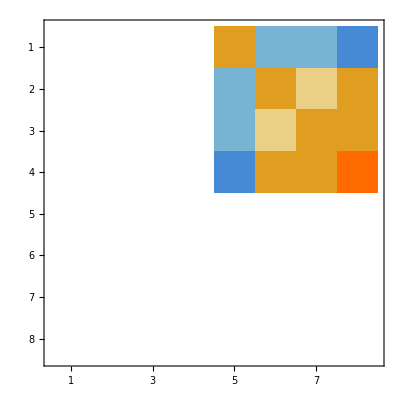

```mathematica
MatrixPlot[%60]
```

```mathematica
expandedExpr = Expand@result[[6,2]]
coeffMatrix=CoefficientArrays[expandedExpr,{x1,x2,x3,x4,y1,y2,y3,y4}][[3]]
MatrixForm[coeffMatrix]
```

(x1 y1)/12-(x2 y1)/24-(x3 y1)/24-(x4 y1)/12-(x1 y2)/24+(x2 y2)/12+(x3 y2)/24+(x4 y2)/12-(x1 y3)/24+(x2 y3)/24+(x3 y3)/12+(x4 y3)/12-(x1 y4)/12+(x2 y4)/12+(x3 y4)/12+(x4 y4)/6

SparseArray[…]

```mathematica
X = {x1,x2,x3,x4,y1,y2,y3,y4}
coeffMatrix=CoefficientArrays[expandedExpr,X][[3]]
coefs = Normal[coeffMatrix]
Expand[X . coefs .Xᵀ]
```

{x1,x2,x3,x4,y1,y2,y3,y4}

SparseArray[…]

{{0,0,0,0,1/12,-1/24,-1/24,-1/12},{0,0,0,0,-1/24,1/12,1/24,1/12},{0,0,0,0,-1/24,1/24,1/12,1/12},{0,0,0,0,-1/12,1/12,1/12,1/6},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

(x1 y1)/12-(x2 y1)/24-(x3 y1)/24-(x4 y1)/12-(x1 y2)/24+(x2 y2)/12+(x3 y2)/24+(x4 y2)/12-(x1 y3)/24+(x2 y3)/24+(x3 y3)/12+(x4 y3)/12-(x1 y4)/12+(x2 y4)/12+(x3 y4)/12+(x4 y4)/6

```mathematica
Normal[CoefficientArrays[%78,{y1,y2,y3,y4}]]
```

{{y1/12-y2/24-y3/24-y4/12,-y1/24+y2/12+y3/24+y4/12,-y1/24+y2/24+y3/12+y4/12,-y1/12+y2/12+y3/12+y4/6}}

```mathematica
result
```

{{x^2,1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))},{y^2,1/12 (y1^2+y2^2+y3^2+2 y3 y4+2 y4^2+y2 (y3+2 y4)-y1 (y2+y3+2 y4))},{z^2,1/12 (z1^2+z2^2+z3^2+2 z3 z4+2 z4^2+z2 (z3+2 z4)-z1 (z2+z3+2 z4))},{y z,1/24 (-y3 z1-2 y4 z1+y3 z2+2 y4 z2+2 y3 z3+2 y4 z3+y1 (2 z1-z2-z3-2 z4)+2 y3 z4+4 y4 z4+y2 (-z1+2 z2+z3+2 z4))},{x z,1/24 (-x3 z1-2 x4 z1+x3 z2+2 x4 z2+2 x3 z3+2 x4 z3+x1 (2 z1-z2-z3-2 z4)+2 x3 z4+4 x4 z4+x2 (-z1+2 z2+z3+2 z4))},{x y,1/24 (-x3 y1-2 x4 y1+x3 y2+2 x4 y2+2 x3 y3+2 x4 y3+x1 (2 y1-y2-y3-2 y4)+2 x3 y4+4 x4 y4+x2 (-y1+2 y2+y3+2 y4))}}

```mathematica
result[[1]]
```

{x^2,1/12 (x1^2+x2^2+x3^2+2 x3 x4+2 x4^2+x2 (x3+2 x4)-x1 (x2+x3+2 x4))}

```mathematica
X={x1,x2,x3,x4};
Y={y1,y2,y3,y4};
Z = {z1,z2,z3,z4};


xxcoeffMatrix=Table[Coefficient[Coefficient[result[[1,2]]*12,X[[i]]],X[[j]]],{i,1,4},{j,1,4}]

yzcoeffMatrix=Table[Coefficient[Coefficient[result[[4,2]]*24,Y[[i]]],Z[[j]]],{i,1,4},{j,1,4}];
xzcoeffMatrix=Table[Coefficient[Coefficient[result[[5,2]]*24,X[[i]]],Z[[j]]],{i,1,4},{j,1,4}];
xycoeffMatrix=Table[Coefficient[Coefficient[result[[6,2]]*24,X[[i]]],Y[[j]]],{i,1,4},{j,1,4}];

yzcoeffMatrix//MatrixForm
 xzcoeffMatrix//MatrixForm
xycoeffMatrix//MatrixForm
```

{{0,-1,-1,-2},{-1,0,1,2},{-1,1,0,2},{-2,2,2,0}}

(2 | -1 | -1 | -2
-1 | 2 | 1 | 2
-1 | 1 | 2 | 2
-2 | 2 | 2 | 4)

(2 | -1 | -1 | -2
-1 | 2 | 1 | 2
-1 | 1 | 2 | 2
-2 | 2 | 2 | 4)

(2 | -1 | -1 | -2
-1 | 2 | 1 | 2
-1 | 1 | 2 | 2
-2 | 2 | 2 | 4)

```mathematica
i^2
```

i^2

{{1,-1,-1,-2},{0,1,1,2},{0,0,1,2},{0,0,0,2}}

```mathematica
xxcoeffMatrix = Normal[CoefficientArrays[result[[1,2]]*12,X][[3]]]
Expand[(1/12) X.xxcoeffMatrix.Xᵀ]
 Expand[result[[1,2]]]
```

{{1,-1,-1,-2},{0,1,1,2},{0,0,1,2},{0,0,0,2}}

x1^2/12-(x1 x2)/12+x2^2/12-(x1 x3)/12+(x2 x3)/12+x3^2/12-(x1 x4)/6+(x2 x4)/6+(x3 x4)/6+x4^2/6

x1^2/12-(x1 x2)/12+x2^2/12-(x1 x3)/12+(x2 x3)/12+x3^2/12-(x1 x4)/6+(x2 x4)/6+(x3 x4)/6+x4^2/6

```mathematica
Expand[X . coeffMatrix.Yᵀ]
```

2 x1 y1-x2 y1-x3 y1-2 x4 y1-x1 y2+2 x2 y2+x3 y2+2 x4 y2-x1 y3+x2 y3+2 x3 y3+2 x4 y3-2 x1 y4+2 x2 y4+2 x3 y4+4 x4 y4

```mathematica
expandedExpr
```

(x1 y1)/12-(x2 y1)/24-(x3 y1)/24-(x4 y1)/12-(x1 y2)/24+(x2 y2)/12+(x3 y2)/24+(x4 y2)/12-(x1 y3)/24+(x2 y3)/24+(x3 y3)/12+(x4 y3)/12-(x1 y4)/12+(x2 y4)/12+(x3 y4)/12+(x4 y4)/6

```mathematica
coeffMatrix//MatrixForm
```

(2 | -1 | -1 | -2
-1 | 2 | 1 | 2
-1 | 1 | 2 | 2
-2 | 2 | 2 | 4)